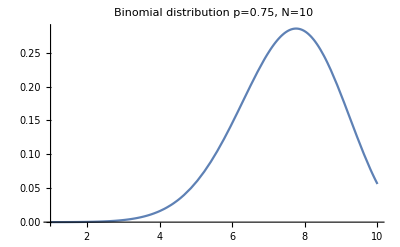

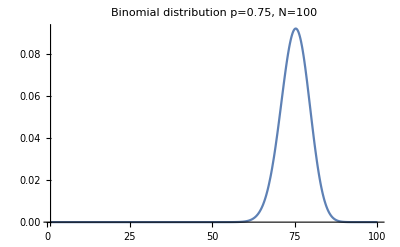

7

71

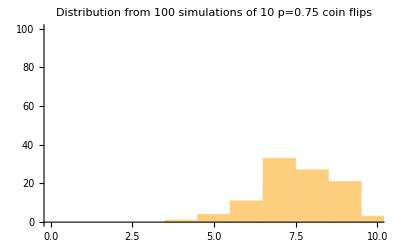

```mathematica
P[N_, x_, p_] := Binomial[N, x] p^x (1-p)^(N- x)
PlotP[N_] :=Plot[P[N, x, 0.75], {x, 1, N}, PlotRange->Full, PlotLabel->"Binomial distribution p=0.75, N=" <> ToString[N]]
PlotP[10]
PlotP[100]

Generator[N_] := If[# >0, 1, 0] &/@ RandomInteger[{0,3}, N]
testGenerator10 = Total[Generator[10]]
testGenerator100 = Total[Generator[100]]
PlotHistogram[N_, Trials_] := Histogram[Table[Total[Generator[N]], {i, Trials}], {1}, PlotRange->{{0, N},{0, Trials}},  PlotLabel-> "Distribution from " <> ToString[Trials]  <> " simulations of 10 p=0.75 coin flips"]
PlotHistogram[10, 100]
```